# Plotting Solutions of ODEs

Informal Theorem
An ODE y'=f(t,y(t)) with an initial condition y'(t_0)=y_0 has a unique solution on some interval around t_0 if f:ℝ×ℝ^n→ℝ^n is smooth.

I will plot a solution to the Rosseler ODE system 
	-Graphics-	
to demonstrate how to compute and plot  a solution. For more information see the wikipedia page 
https://en.wikipedia.org/wiki/R%C3%B6ssler_attractor

```mathematica
Clear[y,t,f,a,b,c]
{a,b,c}={0.2,0.2,5.7};
t0=1.2; TMax=123;
y0={1,2,3};
f[t_,{x_,y_,z_}]:= {-y-z,x+ a y, b  + z(x-c)}
ySol = NDSolveValue[{y'[t]==f[t,y[t]],y[t0]==y0},y,{t,0, TMax}];
ParametricPlot3D[ySol[t],{t,0,TMax},PlotRange->All,PlotPoints->123]
```

-Graphics3D-

There are lots of ways to plot solutions in 3D

```mathematica
ySol[1.205]
```

{0.975155,2.00694,2.93113}

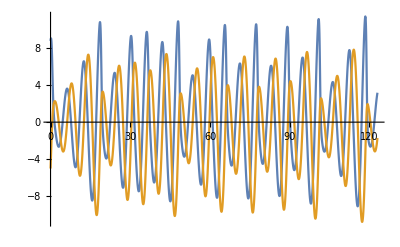

```mathematica
Plot[{ySol[t][[1]],ySol[t][[2]]},{t,0,TMax},PlotRange->All]
```

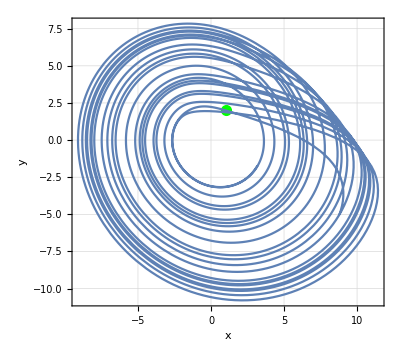

```mathematica
x=2;
ParametricPlot[ySol[t]⟦{1,2}⟧,
{t,0,TMax},PlotRange->All,
Prolog->{Green,PointSize[0.02],Point[y0⟦{1,2}⟧]},
Frame->True,
GridLines->Automatic,
FrameStyle->Directive[Thick,Purple],
AxesStyle->Directive[Thick,Dashed,Magenta],
FrameLabel->{"x","y"}]
```

```mathematica
ySol[12]
```

{5.69984,-3.36871,0.121335}